## July 2020 - Revised calculations for ^135 Pr

## Computing the Contour Plots and the Triaxial Potential for the nucleus

### Constants

```mathematica
j13=13/2;
j11=11/2;
spinValue=19/2;
theta1=-30*π/180;
theta2=-70*π/180;
```

### Formulas

```mathematica
j1[j_,θ_]:=j*Cos[θ];
j2[j_,θ_]:=j*Sin[θ];
Afct[I_,a1_,a2_,j_,θ_]:=a2*(1-j2[j,θ]/I)-a1;
ufct[I_,a1_,a2_,a3_,j_,θ_]:=(a3-a1)/Afct[I,a1,a2,j,θ];
v0fct[I_,a1_,a2_,j_,θ_]:=-(a1*j1[j,θ])/Afct[I,a1,a2,j,θ];
kfct[I_,a1_,a2_,a3_,j_,θ_]:=Sqrt[ufct[I,a1,a2,a3,j,θ]];
IF[moi_]:=1/(2*moi);
```

### Parametric constants k

```mathematica
k9010030=kfct[spinValue,IF[90],IF[100],IF[30],j13,theta1];
k891248=kfct[spinValue,IF[89],IF[12],IF[48],j11,-71*π/180];
k354020=kfct[spinValue,IF[35],IF[40],IF[20],j13,theta2];
k152040=kfct[spinValue,IF[10],IF[20],IF[40],j13,theta2];
k401020=kfct[spinValue,IF[40],IF[10],IF[20],j13,theta2];
kValues={k9010030,k891248,k354020,k152040,k401020};
v9010030=v0fct[spinValue,IF[90],IF[100],j13,theta1];
v891248=v0fct[spinValue,IF[89],IF[12],j11,-71*π/180];
v354020=v0fct[spinValue,IF[35],IF[40],j13,theta2];
v152040=v0fct[spinValue,IF[10],IF[20],j13,theta2];
v401020=v0fct[spinValue,IF[40],IF[10],j13,theta2];
vValues={v9010030,v891248,v354020,v152040,v401020};
```

### Testing the numerical parameter consistency with Raduta’s values

```mathematica
Do[Print[N[kValues[[i]]]],{i,1,Length[kValues]}]
```

3.10165

0.285536

1.30919

2.04965

0.423646

### Generate the q-values for plotting the potential

```mathematica
kTest=0.3;
qValues=Table[q,{q,-8,8,0.1}];
fiValues[q_,k_]:=Table[JacobiAmplitude[q[[i]],k^2],{i,1,Length[q]}];
```

### Jacobi Functions - Functions for the elliptic variables

```mathematica
fiVar[q_,k_]:=JacobiAmplitude[q,k^2];
```

### Potential expression

```mathematica
vRotor[I_,q_,k_,v_]:=(I(I+1)k^2+v^2)Sin[fiVar[q,k]]^2+(2I+1)v*Cos[fiVar[q,k]]*√(1-k^2 Sin[fiVar[q,k]]^2);
```

```mathematica
rotorPlot[I_,i1_,i2_,i3_,j_,θ_]:=Plot[vRotor[I,q,kfct[I,IF[i1],IF[i2],IF[i3],j,θ],v0fct[I,IF[i1],IF[i2],j,θ]],{q,-8,8},AspectRatio->0.8,Frame->True,Axes->False,PlotStyle->{Red,Thick},LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},FrameLabel->{"q [rad]","V(q) [ℏ^2]"},(*PlotLegends->Placed[{"I=19/2"},{0.15,0.85}],*)FrameStyle->Directive[Black,Thick],Epilog->Inset[Style[StringTemplate["θ=(``)^o"][θ*180/π],18,Bold,Black,FontFamily->"Times New Roman"],Scaled[{0.5,0.15}]],FrameTicks->{{Automatic,None},{{-8,-4,0,4,8},None}},PlotRange->All];
```

## Graphical representations for the Triaxial Potential - all cases

### Case: 90 100 30 -30

```mathematica
Print[N[Afct[spinValue,IF[90],IF[100],13/2,-30*π/180]]]
```

0.00115497

```mathematica
Print[N[kfct[spinValue,IF[90],IF[100],IF[30],13/2,-30*π/180]]]
```

3.10165

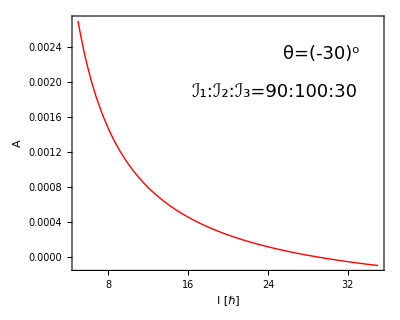

```mathematica
Plot[Afct[s,IF[90],IF[100],13/2,-30*π/180],{s,5,35},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"I [ℏ]","A"},LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},PlotStyle->{Thick,Red},AspectRatio->0.8,Epilog->{Inset[Style[StringTemplate["ℐ_1:ℐ_2:ℐ_3=``:``:````"][90,100,30],18,Italic,FontFamily->"Times New Roman"],Scaled[{0.65,0.7}]],Inset[Style[StringTemplate["θ=(``)^o"][-30],18,Italic,FontFamily->"Times New Roman"],Scaled[{0.8,0.85}]]}]
```

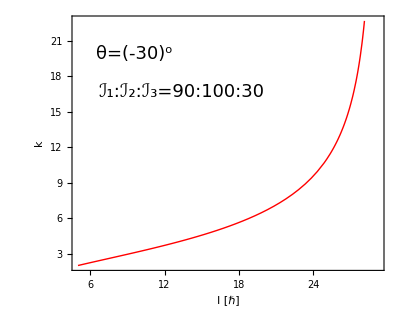

```mathematica
Plot[kfct[s,IF[90],IF[100],IF[30],13/2,-30*π/180],{s,5,30},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"I [ℏ]","k"},LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},PlotStyle->{Thick,Red},AspectRatio->0.8,Epilog->{Inset[Style[StringTemplate["ℐ_1:ℐ_2:ℐ_3=``:``:````"][90,100,30],18,Italic,FontFamily->"Times New Roman"],Scaled[{0.35,0.7}]],Inset[Style[StringTemplate["θ=(``)^o"][-30],18,Italic,FontFamily->"Times New Roman"],Scaled[{0.2,0.85}]]},PlotRange->Automatic]
```

### Create table with condition for the parameters: A and k must be positive

```mathematica
optimalCondition[a1_,a2_,a3_,j_,θ_]:=Table[If[Afct[spin,a1,a2,j,θ]≥0&&kfct[spin,a1,a2,a3,j,θ]≥0,1,0],{spin,5.5,22.5,2}];
checkParams[a1_,a2_,a3_,j_,θ_]:=If[AllTrue[optimalCondition[a1,a2,a3,j,θ],#==1&],1,"INVALID"];
```

### Only plot the triaxial potential if the parameters are consistent with the positivity condition of the inertial factor A and the constant factor k

```mathematica
potentialPlot[I_,a1_,a2_,a3_,j_,θ_]:=Plot[vRotor[I,q,kfct[I,a1,a2,a3,j,θ],v0fct[I,a1,a2,j,θ]],{q,-8,8},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"V(q) [ℏ^2]","q [rad]"},LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},PlotStyle->{Thick,Red},AspectRatio->0.8];
plotOK[I_,a1_,a2_,a3_,j_,θ_]:=If[checkParams[a1,a2,a3,j,θ]==1,Show[potentialPlot[I,a1,a2,a3,j,θ]],"INVALID"];
```

```mathematica
Manipulate[optimalCondition[IF[i1],IF[i2],IF[i3],j13,theta*π/180],{i1,1,120,1},{i2,1,120,1},{i3,1,120,1},{theta,-180,180}]
```

```mathematica
Manipulate[plotOK[19/2,IF[i1],IF[i2],IF[i3],j13,theta*π/180],{i1,1,120,1},{i2,1,120,1},{i3,1,120,1},{theta,-180,180}]
```

```mathematica
Manipulate[rotorPlot[19/2,i1,i2,i3,j13,theta*π/180],{i1,1,120,1},{i2,1,120,1},{i3,1,120,1},{theta,-180,180}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

## Potential good cases:

### I2-maximal moi:

#### Prams: 85, 100, 65, 13/2, -80

#### Potential

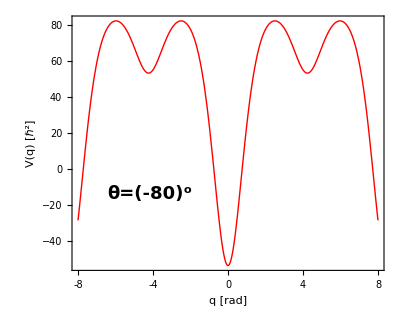

```mathematica
rotorPlot[19/2,85,100,65,j13,-80*π/180]
```

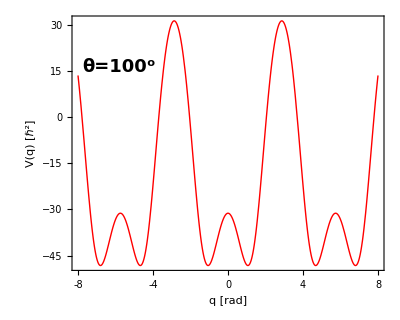

```mathematica
rotorPlot[19/2,85,100,65,j13,100*π/180]
```

### I2-maximal moi:

#### Params: 35, 40, 20, 13/2, -105

#### Potential

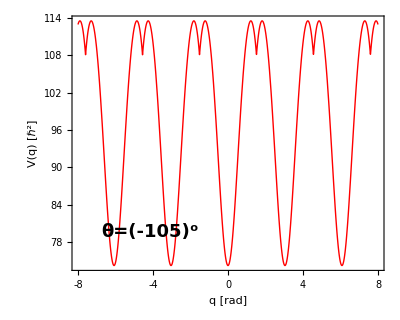

```mathematica
rotorPlot[19/2,35,40,20,j13,-105*π/180]
```

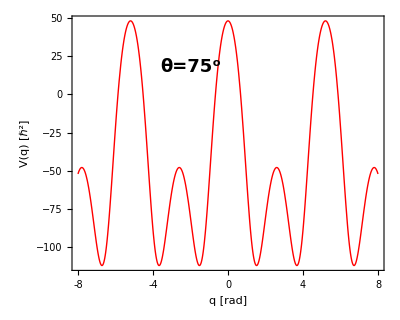

```mathematica
rotorPlot[19/2,35,40,20,j13,75*π/180]
```

### I1-maximal moi:

#### Params: 89, 12, 48, 11/2, -71

#### Potential

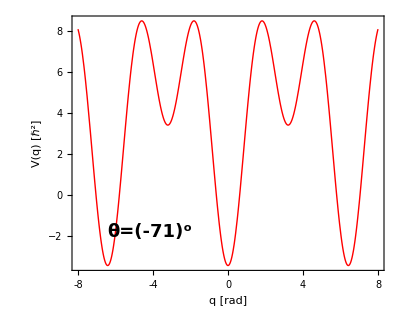

```mathematica
rotorPlot[19/2,89,12,48,j11,-71*π/180]
```

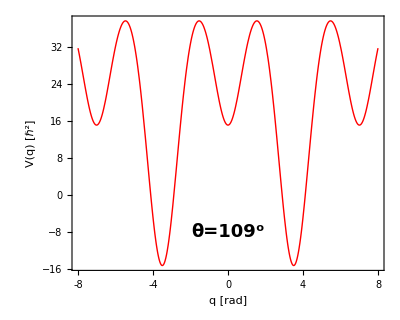

```mathematica
rotorPlot[19/2,89,12,48,j11,(-71+180)*π/180]
```

### I3-maximal moi:

#### **TO BE CALCULATED**